# Revised Deformation Parameters

## 2-axis

### Constants

```mathematica
j11=11/2;
```

### Formulas

```mathematica
j1[j_,θ_]:=j*Cos[θ];
j2[j_,θ_]:=j*Sin[θ];
Afct[I_,a1_,a2_,j_,θ_]:=a2*(1-j2[j,θ]/I)-a1;
ufct[I_,a1_,a2_,a3_,j_,θ_]:=(a3-a1)/Afct[I,a1,a2,j,θ];
v0fct[I_,a1_,a2_,j_,θ_]:=-(a1*j1[j,θ])/Afct[I,a1,a2,j,θ];
kfct[I_,a1_,a2_,a3_,j_,θ_]:=Sqrt[ufct[I,a1,a2,a3,j,θ]];
IF[moi_]:=1/(2*moi);
```

### Jacobi Functions - Functions for the elliptic variables

```mathematica
fiVar[q_,k_]:=JacobiAmplitude[q,k^2];
```

### Potential expression

```mathematica
vRotor[I_,q_,k_,v_]:=(I(I+1)k^2+v^2)Sin[fiVar[q,k]]^2+(2I+1)v*Cos[fiVar[q,k]]*√(1-k^2 Sin[fiVar[q,k]]^2);
```

```mathematica
rotorPlot[I_,i1_,i2_,i3_,j_,θ_]:=Plot[vRotor[I,q,kfct[I,IF[i1],IF[i2],IF[i3],j,θ],v0fct[I,IF[i1],IF[i2],j,θ]],{q,-8,8},AspectRatio->0.8,Frame->True,Axes->False,PlotStyle->{Red,Thick},LabelStyle->{18,Bold,Black,FontFamily->"Times New Roman"},FrameLabel->{"q [rad]","V(q) [ℏ^2]"},(*PlotLegends->Placed[{"I=19/2"},{0.15,0.85}],*)FrameStyle->Directive[Black,Thick],Epilog->Inset[Style[StringTemplate["θ=(``)^o"][θ*180/π],18,Bold,Black,FontFamily->"Times New Roman"],Scaled[{0.15,0.75}]],FrameTicks->{{Automatic,None},{{-8,-4,0,4,8},None}},PlotRange->All];
```

## Create tables with valid A’s and k’s

```mathematica
ATable[i1_,i2_,j_,θ_]:=Table[Afct[spin,IF[i1],IF[i2],j,θ*π/180],{spin,5.5,22.5,2}];
Avalid[i1_,i2_,j_,θ_]:=If[AllTrue[ATable[i1,i2,j,θ],#≥0.0&],{1,"OK"},{0,ATable[i1,i2,j,θ]}];
```

```mathematica
(*Manipulate[Avalid[i1,i2,j11,θ],{i1,1,120,1},{i2,1,120,1},{θ,-180,180,1}]*)
```

```mathematica
kTable[i1_,i2_,i3_,j_,θ_]:=Table[kfct[spin,IF[i1],IF[i2],IF[i3],j,θ*π/180],{spin,5.5,22.5,2}];
kvalid[i1_,i2_,i3_,j_,θ_]:=If[AllTrue[kTable[i1,i2,i3,j,θ],#≥0.0&&#<1.0&&Im[#]==0&],{1,"OK"},{0,kTable[i1,i2,i3,j,θ]}];
```

```mathematica
(*Manipulate[kvalid[i1,i2,i3,j11,θ],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{θ,-180,180,1}]*)
```

```mathematica
optimalCondition[i1_,i2_,i3_,j_,θ_]:=If[kvalid[i1,i2,i3,j,θ][[1]]==1&&Avalid[i1,i2,j,θ][[1]]==1,{1,"OK"},{0,kTable[i1,i2,i3,j,θ],ATable[i1,i2,j,θ]}];
```

```mathematica
(*Manipulate[optimalCondition[i1,i2,i3,j11,θ],{i1,1,120,1},{i2,1,120,1},{i3,1,120,1},{θ,-180,180,1}]*)
```

```mathematica
(*For[i1=1,i1≤120,i1++,For[i2=1,i2≤12,i2++,For[i3=1,i3≤120,i3++,For[θ=-180,θ≤180,θ++,If[optimalCondition[i1,i2,i3,j11,θ],Print[i1," ",i2," ",i3," ",θ]]]]]]*)
```

## Params: 90 100 80 11/2 -80

```mathematica
plotOK[I_,i1_,i2_,i3_,j_,θ_]:=If[optimalCondition[i1,i2,i3,j,θ][[1]]==1,Show[rotorPlot[I,i1,i2,i3,j,θ*π/180]],"INVALID PLOT"];
```

```mathematica
Manipulate[plotOK[spin,90,100,80,j11,-80],{spin,5.5,22.5,2}]
```

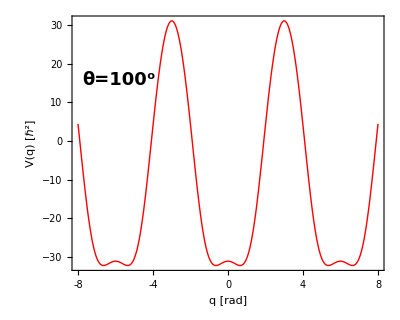

```mathematica
rotorPlot[19/2,90,100,80,j11,100*π/180]
```

```mathematica
Table[vRotor[
```